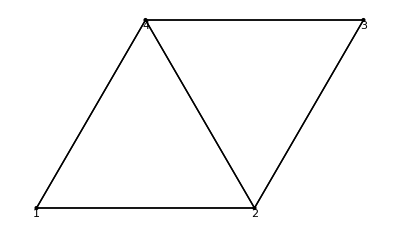

{{F[1,2]→-1/(2 √3),F[1,4]→1/(√3),F[2,3]→-2/(√3),F[2,4]→-1/(√3),F[3,4]→1/(√3),px[1]→0,py[1]→-1/2,py[2]→3/2}}

```mathematica
Clear[Palicje]
SetDirectory["~/faks/mm/"];
Needs["Palicje`"];
vozlisca = {{0,0},{1,0},{3/2,Sqrt[3]/2},{1/2,Sqrt[3]/2}};
povezave = {{2,4},{1,3,4},{2,4},{1,2,3}};
podpore={{1,{px[1],py[1]}},{2,{0,py[2]}}};
obremenitve = {{3,{0,-1}}};
NarisiPalicje[vozlisca,povezave]
enacbe = GenerirajEnacbe[vozlisca, povezave, obremenitve, podpore];
neznanke = GenerirajNeznanke[povezave,podpore];
Solve[enacbe,neznanke]
```

```mathematica
?Palicje`*
```

```mathematica
?F
??GenerirajEnacbe
```

Neznanka, uporabljena za notranje sile.

Vrne sistem ravnovesnih enačb za vsa vozlišča, upoštevajoč obremenitve, podpore in notranje sile

GenerirajEnacbe[Private`Vozlisca_,Private`Povezave_,Private`Obremenitve_,Private`Podpore_]:=Module[{Private`Sistem,Private`SileVozlisca},Private`SileVozlisca=Table[SileNaVozlisce[Private`i,Private`Vozlisca,Private`Povezave],{Private`i,1,Length[Private`Vozlisca]}];DodajObremenitve[Private`Obremenitve,Private`SileVozlisca];DodajObremenitve[Private`Podpore,Private`SileVozlisca];Flatten[Table[Thread[Private`SileVozlisca⟦Private`i⟧==0],{Private`i,Length[Private`Vozlisca]}]]]